```mathematica
numberOfTrials = 0; 
probability = 1;
scorePerThrow = 1; 
results = List[];
iterator = 0; 
innerIter = 0; 
origBaseScore = 400; 
origBaseTarget = 400; 
target =origBaseTarget;
r=0;

While [iterator < 400, 
target = target + 0.01;   
runningProbability = 0; 
While [ innerIter < 10,
	(*Print["Ran Inner Iterator"];*)
	baseScore = origBaseScore;
	(*Print["Base Score is " + baseScore];*)
	ratio = target/origBaseScore; 
	While [ target > baseScore ∧ baseScore > 0,
			(*Print[r++];*)
			If [ RandomInteger[1] == 0,
				baseScore = baseScore + scorePerThrow,
				baseScore  = baseScore - scorePerThrow
			   ];
			probability = probability * 0.6; 
		];
	(*Print[runningProbability + "running probability"];
	Print[probability + "momentProbability"];*)
	runningProbability = runningProbability + probability; 

	probability = 1; 
	innerIter++;
	];
(*Print[runningProbability + "Running Probability is" ];*)
innerIter = 0; 
totalProbability = runningProbability/10; 
(*Print[totalProbability];*)
runningProbability = 0; 
 
	(*Print["ONE HIT"]*)
	AppendTo[results, {target,totalProbability}]

iterator++; 
]
results
```

{{400.01,0.323101},{400.02,0.241276},{400.03,0.389513},{400.04,0.408799},{400.05,0.313511},{400.06,0.212192},{400.07,0.3816},{400.08,0.360726},{400.09,0.316562},{400.1,0.291154},{400.11,0.189153},{400.12,0.243854},{400.13,0.248654},{400.14,0.307599},{400.15,0.277152},{400.16,0.382608},{400.17,0.42},{400.18,0.180856},{400.19,0.481008},{400.2,0.300494},{400.21,0.220316},{400.22,0.381608},{400.23,0.269739},{400.24,0.312939},{400.25,0.152948},{400.26,0.238752},{400.27,0.410976},{400.28,0.327199},{400.29,0.305855},{400.3,0.241202},{400.31,0.405999},{400.32,0.420047},{400.33,0.343378},{400.34,0.42},{400.35,0.381963},{400.36,0.275982},{400.37,0.329376},{400.38,0.255915},{400.39,0.330384},{400.4,0.310416},{400.41,0.330431},{400.42,0.272223},{400.43,0.313584},{400.44,0.269756},{400.45,0.367605},{400.46,0.313375},{400.47,0.382609},{400.48,0.283217},{400.49,0.277152},{400.5,0.345999},{400.51,0.241864},{400.52,0.209399},{400.53,0.389376},{400.54,0.482802},{400.55,0.413775},{400.56,0.292245},{400.57,0.323333},{400.58,0.310593},{400.59,0.304815},{400.6,0.329376},{400.61,0.293792},{400.62,0.385538},{400.63,0.444399},{400.64,0.138554},{400.65,0.410976},{400.66,0.301551},{400.67,0.256607},{400.68,0.3244},{400.69,0.385407},{400.7,0.283563},{400.71,0.324762},{400.72,0.368502},{400.73,0.36293},{400.74,0.3432},{400.75,0.427776},{400.76,0.143282},{400.77,0.352114},{400.78,0.284209},{400.79,0.339951},{400.8,0.341952},{400.81,0.438351},{400.82,0.329739},{400.83,0.4032},{400.84,0.445407},{400.85,0.305526},{400.86,0.361014},{400.87,0.312576},{400.88,0.323616},{400.89,0.410976},{400.9,0.42},{400.91,0.383101},{400.92,0.269393},{400.93,0.393183},{400.94,0.367599},{400.95,0.344928},{400.96,0.463247},{400.97,0.197568},{400.98,0.323101},{400.99,0.367599},{401.,0.353781},{401.01,0.147917},{401.02,0.0559381},{401.03,0.176265},{401.04,0.0506396},{401.05,0.140265},{401.06,0.138586},{401.07,0.126448},{401.08,0.141947},{401.09,0.0664886},{401.1,0.125094},{401.11,0.0877051},{401.12,0.125626},{401.13,0.178549},{401.14,0.120772},{401.15,0.0722291},{401.16,0.104265},{401.17,0.153363},{401.18,0.19296},{401.19,0.150345},{401.2,0.0801503},{401.21,0.0427843},{401.22,0.0927322},{401.23,0.000180696},{401.24,0.0848979},{401.25,0.108},{401.26,0.134138},{401.27,0.125637},{401.28,0.0979214},{401.29,0.0268222},{401.3,0.0671903},{401.31,0.0908631},{401.32,0.161843},{401.33,0.121406},{401.34,0.21768},{401.35,0.161843},{401.36,0.117858},{401.37,0.0433325},{401.38,0.105098},{401.39,0.115652},{401.4,0.148966},{401.41,0.0510751},{401.42,0.113488},{401.43,0.0858207},{401.44,0.115556},{401.45,0.123244},{401.46,0.14688},{401.47,0.128621},{401.48,0.0813418},{401.49,0.0146961},{401.5,0.158001},{401.51,0.139099},{401.52,0.085786},{401.53,0.144931},{401.54,0.13048},{401.55,0.0652894},{401.56,0.108931},{401.57,0.125705},{401.58,0.131002},{401.59,0.170742},{401.6,0.0783452},{401.61,0.110284},{401.62,0.119021},{401.63,0.269626},{401.64,0.163533},{401.65,0.122718},{401.66,0.117413},{401.67,0.157179},{401.68,0.10319},{401.69,0.0979997},{401.7,0.11256},{401.71,0.15696},{401.72,0.0942949},{401.73,0.127131},{401.74,0.0995996},{401.75,0.0498709},{401.76,0.150241},{401.77,0.18527},{401.78,0.089664},{401.79,0.0482112},{401.8,0.0537142},{401.81,0.146534},{401.82,0.0685649},{401.83,0.0866396},{401.84,0.0635998},{401.85,0.13392},{401.86,0.117936},{401.87,0.158643},{401.88,0.131114},{401.89,0.0778141},{401.9,0.155239},{401.91,0.0982944},{401.92,0.114457},{401.93,0.139192},{401.94,0.0938108},{401.95,0.0729391},{401.96,0.23064},{401.97,0.0573279},{401.98,0.123849},{401.99,0.0712794},{402.,0.0773499},{402.01,0.0155919},{402.02,0.0437434},{402.03,0.0831521},{402.04,0.0521153},{402.05,0.00674242},{402.06,0.0730695},{402.07,0.0432341},{402.08,0.0471377},{402.09,0.0382675},{402.1,0.0133808},{402.11,0.0303899},{402.12,0.0520029},{402.13,0.0537776},{402.14,0.0658573},{402.15,0.0513482},{402.16,0.0449619},{402.17,0.0296564},{402.18,0.00291061},{402.19,0.0299514},{402.2,0.0676464},{402.21,0.0725763},{402.22,0.0470712},{402.23,0.058799},{402.24,0.0460056},{402.25,0.028055},{402.26,0.0216239},{402.27,0.0125909},{402.28,0.0217949},{402.29,0.0432008},{402.3,0.00778121},{402.31,0.00909358},{402.32,0.0443406},{402.33,0.0244001},{402.34,0.0127686},{402.35,0.0325443},{402.36,0.0149714},{402.37,0.0183404},{402.38,0.0983459},{402.39,0.000017211},{402.4,0.0133925},{402.41,0.0442078},{402.42,0.0505267},{402.43,0.0453631},{402.44,0.064351},{402.45,0.0105783},{402.46,0.00774785},{402.47,0.0297859},{402.48,0.00891518},{402.49,0.0658078},{402.5,0.0513411},{402.51,0.00457974},{402.52,0.0442147},{402.53,0.0680928},{402.54,0.00879065},{402.55,0.0382934},{402.56,0.0185293},{402.57,0.040724},{402.58,0.0539063},{402.59,0.0432252},{402.6,0.00128591},{402.61,0.0461792},{402.62,0.0558662},{402.63,0.0119711},{402.64,0.036703},{402.65,0.0537754},{402.66,0.0649336},{402.67,0.075506},{402.68,0.0010747},{402.69,0.0420983},{402.7,0.0184828},{402.71,0.0649411},{402.72,0.0488156},{402.73,0.0216001},{402.74,0.0382069},{402.75,0.0668155},{402.76,0.00466556},{402.77,0.0659384},{402.78,0.0233512},{402.79,0.00791712},{402.8,0.0254541},{402.81,0.0664788},{402.82,0.0541382},{402.83,0.0567523},{402.84,0.0882586},{402.85,0.0445224},{402.86,0.0299353},{402.87,0.04613},{402.88,0.0155526},{402.89,0.0331892},{402.9,0.0295066},{402.91,0.00280556},{402.92,0.00121925},{402.93,0.0464972},{402.94,0.0731642},{402.95,0.0323533},{402.96,0.0755068},{402.97,0.0335637},{402.98,0.0332363},{402.99,0.102591},{403.,0.0729573},{403.01,0.00229575},{403.02,0.02592},{403.03,0.0148623},{403.04,0.00637343},{403.05,0.00363699},{403.06,0.00825314},{403.07,0.0017332},{403.08,0.00660134},{403.09,4.81799×10^-7},{403.1,0.0239745},{403.11,0.0305856},{403.12,0.0194119},{403.13,0.0110432},{403.14,0.0148586},{403.15,0.0212809},{403.16,0.0146396},{403.17,0.00193566},{403.18,0.0136532},{403.19,0.0152448},{403.2,0.0131777},{403.21,0.00211517},{403.22,0.0176261},{403.23,0.00557044},{403.24,0.00250561},{403.25,0.00197698},{403.26,0.0312686},{403.27,0.0240492},{403.28,0.0134737},{403.29,0.0135762},{403.3,0.00954888},{403.31,0.00678578},{403.32,0.00504001},{403.33,0.0436443},{403.34,0.0185264},{403.35,0.0163194},{403.36,0.0176331},{403.37,0.012769},{403.38,0.0131883},{403.39,0.0312077},{403.4,0.013643},{403.41,0.000306391},{403.42,0.0262944},{403.43,0.00307388},{403.44,0.000296042},{403.45,0.0182308},{403.46,0.000682623},{403.47,0.00466614},{403.48,0.00296737},{403.49,0.0200165},{403.5,0.0132567},{403.51,0.0111678},{403.52,0.0290266},{403.53,0.000227856},{403.54,0.014718},{403.55,0.0019116},{403.56,0.0177337},{403.57,0.000156728},{403.58,0.0354704},{403.59,0.00496164},{403.6,0.0136449},{403.61,0.00717772},{403.62,0.0209853},{403.63,0.0131168},{403.64,0.0223697},{403.65,0.0076329},{403.66,0.00344825},{403.67,0.0000898364},{403.68,0.00933167},{403.69,0.013049},{403.7,0.027934},{403.71,0.000463576},{403.72,0.000309861},{403.73,0.0110432},{403.74,0.0110393},{403.75,0.00466566},{403.76,0.026216},{403.77,0.00526018},{403.78,0.0137878},{403.79,0.00527032},{403.8,0.00175804},{403.81,0.0131777},{403.82,0.0148679},{403.83,0.00634707},{403.84,0.0193836},{403.85,0.00642364},{403.86,0.00023799},{403.87,0.0163409},{403.88,0.018233},{403.89,0.0129641},{403.9,0.00133103},{403.91,0.00710517},{403.92,0.00466607},{403.93,0.0146397},{403.94,0.0129605},{403.95,0.0265349},{403.96,0.0214239},{403.97,0.0223314},{403.98,0.00641545},{403.99,0.000605613},{404.,0.0165376}}

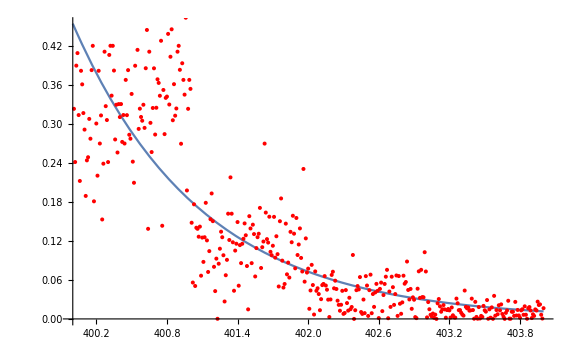

```mathematica
dataPlot = ListPlot[results,PlotRange->All,ImageSize->Large, Joined->False,Frame->True,FrameLabel->{"K (targetScore/BaseScore) ","P(k)","",""}, LabelStyle->{FontSize->14, Directive[Bold,Black]},PlotStyle->{RGBColor[1,0,0],PointSize[0.005]}];
myFit = Fit[results,{0.4^x},x];
fitPlot = Plot[myFit,{x,400,404}];
Show[fitPlot,dataPlot]
```